```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=35;R=2;a=0.5;μ=8/9 Subscript[m, N];
rmax=4.0;dr=0.01;
rlist=Range[0,rmax,dr];
n=Length[rlist]
```

401

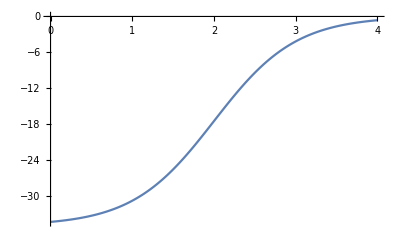

```mathematica
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
KE=-ℏc^2/(2 μ) 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
H0=KE+Vmat;
```

```mathematica
(*{eval,evec}=Eigensystem[H0];
Manipulate[ListPlot[{rlist,evec⟦-i⟧}ᵀ,Joined->True,PlotRange->All],{i,1,n,1}]*)
```

```mathematica
k[En_]:=Sqrt[-(2μ En)/ℏc^2]
```

```mathematica
En=V0/2;En1=1;
```

```mathematica
k[V0/2]
```

0.+0.866633 ⅈ

```mathematica
H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(dr k[En]-1);{eval,evec}=Eigensystem[H];
```

```mathematica
Manipulate[ListLinePlot[{Transpose[{rlist,Abs[evec⟦-i⟧]}]},PlotRange->All],{i,1,n,1}]
```

```mathematica
eval[[-4]]
```

157.661-10.9634 ⅈ

```mathematica
While[Abs[En/En1]≥1.0001||Abs[En/En1]≤0.9999,H=H0;H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(dr k[En]-1);{eval,evec}=Eigensystem[H];En1=En;En=eval[[-1]];]
```

```mathematica
En
```

-7.36002

```mathematica
wave[En_,r_]:=Sin[k[En] r+δ]
```

```mathematica
const[i_]:=evec[[-i,-1]]/wave[eval[[-i]],rmax]
```

```mathematica
(*Manipulate[ListLinePlot[{Transpose[{rlist,evec⟦-i⟧}],Transpose[{Range[rmax,10,dr],const[i] wave[eval[[-i]],Range[rmax,10,dr]]}]},PlotRange->All],{i,1,n,1}]*)
```